```mathematica
GetFormatedScopeMeasurement
```

```mathematica
formatedSidebandData2=GetFormatedScopeMeasurement[sidebandData2⟦1,3⟧];
```

```mathematica
sidebandData2⟦1,3⟧⟦3,3⟧//Length
```

2

```mathematica
convertToFormatedScopeData[rawMeasurement_List]:=Module[{i,j,vecPos,timeBase,formatedData,points,point,t0},
timeBase=1;
vecPos=0;
formatedData={};
For[i=1,i≤ Length[rawMeasurement],i++,
If[Length[rawMeasurement⟦i⟧]>0&&StringQ[rawMeasurement⟦i,1⟧],
If[rawMeasurement⟦i,1⟧=="TimeBase",timeBase=rawMeasurement⟦i,2⟧];
,
If[ListQ[rawMeasurement⟦i,1⟧],vecPos=i;];
];
];
If[vecPos==0,Return[formatedData]];

points=0;
For[i=1,i≤ Length[rawMeasurement⟦vecPos⟧],i++,
points+=Length[rawMeasurement⟦vecPos,i,2⟧];
];

formatedData=Table[{Null,Null},{i,1,points}];

point=1;
For[i=1,i≤Length[rawMeasurement⟦vecPos⟧],i++,
t0=rawMeasurement⟦vecPos,i,1⟧;
For[j=1,j≤Length[rawMeasurement⟦vecPos,i,2⟧],j++,
formatedData⟦point,1⟧=t0+(j-1)*timeBase;
formatedData⟦point,2⟧=rawMeasurement⟦vecPos,i,2,j⟧;
point++;
];

];
formatedData
]
```

```mathematica
Module[{i,j,vecPos,timeBase,formatedData,points,point,t0},
timeBase=1;
vecPos=0;
formatedData={};
For[i=1,i≤ Length[rawMeasurement],i++,
If[Length[rawMeasurement⟦i⟧]>0&&StringQ[rawMeasurement⟦i,1⟧],
If[rawMeasurement⟦i,1⟧=="TimeBase",timeBase=rawMeasurement⟦i,2⟧];
,
If[ListQ[rawMeasurement⟦i,1⟧],vecPos=i;];
];
];
If[vecPos==0,Return[formatedData]];

points=0;
For[i=1,i≤ Length[rawMeasurement⟦vecPos⟧],i++,
points+=Length[rawMeasurement⟦vecPos,i,2⟧];
];

formatedData=Table[{Null,Null},{i,1,points}];

point=1;
For[i=1,i≤Length[rawMeasurement⟦vecPos⟧],i++,
t0=rawMeasurement⟦vecPos,i,1⟧;
For[j=1,j≤Length[rawMeasurement⟦vecPos,i,2⟧],j++,
formatedData⟦point,1⟧=t0+(j-1)*timeBase;
formatedData⟦point,2⟧=rawMeasurement⟦vecPos,i,2,j⟧;
point++;
];

];
formatedData
]//CForm
```

Return(List())

```mathematica
Needs["SymbolicC`"]
```

```mathematica
sidebandData2⟦1,3⟧//Length
```

3

```mathematica
convertToFormatedScopeData[sidebandData2⟦1,3⟧]//Dimensions
```

{1579,2}

```mathematica
formatedSidebandData2//Dimensions
```

{1579,2}

```mathematica
convertToFormatedScopeData[sidebandData2⟦1,3⟧]-formatedSidebandData2
```

{{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.},{-9.6×10^-7,0.}}

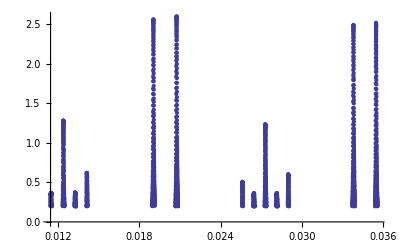

```mathematica
convertToFormatedScopeData[sidebandData2⟦1,3⟧]//ListPlot
```